## Calculations for null geodesics in Schwarzschild and tidal effects in the GW phase

#### geometric units G=1=c are used throughout

## circular null geodesics

#### preliminaries and Hamiltonian

Metric and inverse

```mathematica
metric={{-f[r] ,0,0,0},{0,1/f[r],0,0},{0,0,r^2,0},{0,0,0,r^2 Sin[θ]^2}};
```

```mathematica
inversemetric=Inverse[metric];
```

insert the explicit metric functions

```mathematica
insertmet={f[r]->1-2  MM/(r )};
```

specialize to equatorial orbits, no longer consider θ-motion

```mathematica
equat={θ->Pi/2};
```

coordinates and canonical momenta

```mathematica
coord={t,r,ϕ};
mom={pt,pr,pϕ};
```

construct the Hamiltonian

```mathematica
Hamilt=1/2 Sum[Sum[inversemetric[[i,j]]mom[[i]]mom[[j]],{i,1,3}],{j,1,3}]/.equat
```

1/2 (pϕ^2/r^2-pt^2/f[r]+pr^2 f[r])

#### equations of motion

Hamiltonian equations of motion, the left hand sides are d/dλ (affine parameter) of the coordinates and momenta

```mathematica
eomscoordrhs=Table[D[Hamilt,mom[[i]]],{i,1,3}]
eomsmomrhs=Table[-D[Hamilt,coord[[i]]],{i,1,3}]
```

{-pt/f[r],pr f[r],pϕ/r^2}

{0,1/2 ((2 pϕ^2)/r^3-pr^2 f'[r]-(pt^2 f'[r])/f[r]^2),0}

pt and pϕ remain constant under the evolution, identify with the energy and angular momentum

```mathematica
conserved={pt->-EE,pϕ->LL};
```

write the eoms in terms of these conserved quantities

```mathematica
eomsc=eomscoordrhs/.conserved
eomsp=eomsmomrhs/.conserved
```

{EE/f[r],pr f[r],LL/r^2}

{0,1/2 ((2 LL^2)/r^3-pr^2 f'[r]-(EE^2 f'[r])/f[r]^2),0}

null geodesics: Hamiltonian =0, use to solve for pr^2(E,L,r)

```mathematica
profEL=Solve[(Hamilt/.conserved/.pr->Sqrt[pr2])==0,pr2][[1]]//Apart
```

{pr2→EE^2/f[r]^2-LL^2/(r^2 f[r])}

Aside: for reference, the usual effective potential defined by (dr/dλ)^2=Veff

```mathematica
poten=-Expand[eomsc[[2]]^2]/.r'[t]->0/.pr'[t]->0/.pr->(Sqrt[pr2]/.profEL)/.r[t]->r/.insertmet/.D[insertmet,r]//FullSimplify
```

-EE^2+(LL^2 (-2 MM+r))/r^3

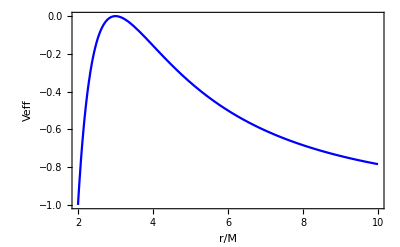

```mathematica
Plot[{poten/.LL->Sqrt[27]/.EE->1/.MM->1},{r,2.,10}, Frame->True, FrameLabel->{"r/M", "Veff", "effective potential for null geodesics"}, PlotStyle->Directive[Blue], LabelStyle->Medium]
```

#### motion in coordinate time

convert to equations in terms of coordinate time evolution

```mathematica
eomscoft=Table[eomsc[[i+1]]/eomsc[[1]],{i,1,2}]
eomspoft=eomsp[[2]]/eomsc[[1]](*/.pr^2->pr2/.profEL*)//FullSimplify
```

{(pr f[r]^2)/EE,(LL f[r])/(EE r^2)}

(f[r] ((2 LL^2)/r^3+(-pr^2-EE^2/f[r]^2) f'[r]))/(2 EE)

now write the eoms fully so that each line == 0

```mathematica
fulleoms={-r'[t]+(eomscoft[[1]]/.insertmet/.r->r[t]/.pr->pr[t]),-ϕ'[t]+(eomscoft[[2]]/.insertmet/.r->r[t]),-pr'[t]+(eomspoft/.insertmet/.D[insertmet,r]/.r->r[t]/.pr->pr[t])}//FullSimplify
```

{(pr[t] (1-(2 MM)/r[t])^2)/EE-r'[t],(LL (-2 MM+r[t]))/(EE r[t]^3)-ϕ'[t],((1-(2 MM)/r[t]) ((2 LL^2)/r[t]^3-(2 MM pr[t]^2)/r[t]^2-(2 EE^2 MM)/(-2 MM+r[t])^2))/(2 EE)-pr'[t]}

#### unstable equilibrium point

solving for the parameters of the saddle point

```mathematica
unstcirc=Solve[{(pr2/.profEL/.insertmet/.r->r[t]/.LL->Sqrt[LL2])==0,(fulleoms[[3]]/.pr[t]->0/.pr'[t]->0/.LL->Sqrt[LL2])==0},{r[t],LL2}][[1]]
```

{r[t]→3 MM,LL2→27 EE^2 MM^2}

and the azimuthal frequency there

```mathematica
omegaunstcirc=Solve[(fulleoms[[2]]/.LL->Sqrt[LL2]/.unstcirc)==0,ϕ'[t]][[1]]//PowerExpand
```

{ϕ'[t]→1/(3 √3 MM)}

equations of motion for the critical angular momentum for numerical evolution (with M=1, E=1, not worrying about writing things in terms of an impact parameter here

```mathematica
fulleomstest=fulleoms/.EE->1/.MM->1/.LL->Sqrt[27]
```

{pr[t] (1-2/r[t])^2-r'[t],(3 √3 (-2+r[t]))/r[t]^3-ϕ'[t],1/2 (-2/(-2+r[t])^2+54/r[t]^3-(2 pr[t]^2)/r[t]^2) (1-2/r[t])-pr'[t]}

numerical results to plot the phase plane for different closest approaches to the saddle point

```mathematica
ch=NDSolve[{fulleomstest[[1]]==0,fulleomstest[[3]]==0, r[0]==2.98, pr[0]==0},{r[t],pr[t]},{t,-20,20}][[1]];
ch1=NDSolve[{fulleomstest[[1]]==0,fulleomstest[[3]]==0, r[0]==3.02, pr[0]==0},{r[t],pr[t]},{t,-20,20}][[1]];
```

```mathematica
chx=NDSolve[{fulleomstest[[1]]==0,fulleomstest[[3]]==0, r[0]==2.999, pr[0]==0},{r[t],pr[t]},{t,-50,50}][[1]];
ch1x=NDSolve[{fulleomstest[[1]]==0,fulleomstest[[3]]==0, r[0]==3.001, pr[0]==0},{r[t],pr[t]},{t,-50,50}][[1]];
```

```mathematica
cha=NDSolve[{fulleomstest[[1]]==0,fulleomstest[[3]]==0, r[0]==2.96, pr[0]==0},{r[t],pr[t]},{t,-10,10}][[1]];
ch1a=NDSolve[{fulleomstest[[1]]==0,fulleomstest[[3]]==0, r[0]==3.04, pr[0]==0},{r[t],pr[t]},{t,-10,10}][[1]];
```

```mathematica
Show[ParametricPlot[{r[t],pr[t]}/.ch1a,{t,-8,8}, AspectRatio->1/2, PlotStyle->Directive[Green]],ParametricPlot[{r[t],pr[t]}/.cha,{t,-8,8}, AspectRatio->1/2,PlotStyle->Directive[Green]],
ParametricPlot[{r[t],pr[t]}/.ch1x,{t,-28,28}, AspectRatio->1/2, PlotStyle->Directive[Blue]],ParametricPlot[{r[t],pr[t]}/.chx,{t,-28,28}, AspectRatio->1/2,PlotStyle->Directive[Blue]],ParametricPlot[{r[t],pr[t]}/.ch1,{t,-15,15}, AspectRatio->1/2, PlotStyle->Directive[Cyan]],ParametricPlot[{r[t],pr[t]}/.ch,{t,-15,15}, AspectRatio->1/2,PlotStyle->Directive[Cyan]], PlotRange->{{2.93,3.07},{-0.13,.13}}, Frame->True, AxesOrigin->{3,0}, FrameLabel->{"r/M", "pr","phase plane of null geodesics close to the saddle point"}, LabelStyle->Medium]
```

#### small deviations from equilibrium

```mathematica
smallpert={r[t]->(r[t]/.unstcirc)+δ r1[t], pr[t]->δ pr1[t], ϕ'[t]->(ϕ'[t]/.omegaunstcirc)+δ ω[t]};
```

linarized equations of motion

```mathematica
expanded=Normal[Series[fulleoms/.LL->Sqrt[LL2]/.smallpert/.D[smallpert,t]/.unstcirc/.omegaunstcirc,{δ,0,1}]]//PowerExpand
```

{δ (pr1[t]/(9 EE)-r1'[t]),-δ ω[t],δ ((EE r1[t])/(3 MM^2)-pr1'[t])}

first, check that a direct solution yields the expected behavior (c.f. the phase portrait) with a specific decay rate (seen to be 1/(3 √3 MM)):

```mathematica
checkrpr=DSolve[{expanded[[1]]==0,expanded[[3]]==0},{r1[t],pr1[t]},t]//FullSimplify
```

{{pr1[t]→C[1] Cosh[t/(3 √3 MM)]+(√3 EE C[2] Sinh[t/(3 √3 MM)])/MM,r1[t]→C[2] Cosh[t/(3 √3 MM)]+(MM C[1] Sinh[t/(3 √3 MM)])/(√3 EE)}}

The linear stability matrix denoted by L in the exercise sheet, dropping the zero line)

```mathematica
matrix={{0,r1'[t]+expanded[[1]]},{pr1'[t]+expanded[[3]],0}}/.δ->1/.pr1[t]->1/.r1[t]->1
```

{{0,1/(9 EE)},{EE/(3 MM^2),0}}

eigenvalues

```mathematica
Eigenvalues[matrix]//FullSimplify
```

{-1/(3 √3 MM),1/(3 √3 MM)}

these values characterize the divergence towards and away from the saddle point (c.f. the phase portrait), and we will interpret them as connected to the imaginary part of the QNM frequency

#### approximate link with QNMs

QNMs results

since the linear perturbation to ω vanishes, the frequency is that of the LR orbit, and increases linearly with the multipolar order since the perturbation modes go as e^(-i (ω t-l ϕ)) (independent of the azimuthal number m in spherical symmetry)

```mathematica
wzero=l*ϕ'[t]/.omegaunstcirc
```

l/(3 √3 MM)

the Lyapunov exponents are the +- eigenvalues. We take only the divergent ones since those are the trajectories that can move outwards to the distant observer

```mathematica
gamm=Eigenvalues[matrix][[2]]//N;
```

from HW3, we have a connection between properties of a damped oscillator (ω0, γ) and the real and imaginary parts of the QNM frequencies (ωR, ωI):

```mathematica
wreal[l_]=1/2*Sqrt[4 wzero^2-gamm^2]
```

1/2 √(-0.037037/MM^2+(4 l^2)/(27 MM^2))

expand for large l

```mathematica
wreal1[l_]=Normal[Series[wreal[l],{l,∞,0}]]//PowerExpand
```

l/(3 √3 MM)

tabulating the numerical values for ωR

```mathematica
tab={.3737,.5994,.8092};
```

```mathematica
wR=Table[MM wreal1[i],{i,2,4}]//PowerExpand//FullSimplify//N
```

{0.3849,0.57735,0.7698}

take the % difference to numerics

```mathematica
Table[-((wR[[i]])-tab[[i]])/tab[[i]]*100,{i,1,3}]
```

{-2.9971,3.67863,4.86896}

we see that the approximation works quite well, even for these low-l values

for the decay rate, we also had a relation from HW3 between that of an oscillator and the imaginary part of the QNM frequency:

```mathematica
wI=MM gamm/2
```

0.096225

tabulating the numerical values

```mathematica
tabwI={.0889,.0927,.0941};
```

the % difference

```mathematica
Table[-(wI-tabwI[[i]])/tabwI[[i]]*100,{i,1,3}]
```

{-8.23965,-3.80264,-2.25828}

here we actually see the expected trend that the approximation becomes better for higher l-values (lower wavelength modes)

## tidal phasing

#### preliminaries and definitions

```mathematica
vecn={Cos[ϕ],Sin[ϕ],0};
```

```mathematica
nij=Outer[Times,vecn,vecn];
```

```mathematica
nijSTF=nij-1/3 IdentityMatrix[3]Tr[nij]//FullSimplify
```

{{1/6 (1+3 Cos[2 ϕ]),Cos[ϕ] Sin[ϕ],0},{Cos[ϕ] Sin[ϕ],1/6 (1-3 Cos[2 ϕ]),0},{0,0,-1/3}}

Newtonian quadrupolar tidal tensor

```mathematica
Eij=-3 m2 nijSTF/r^3;
```

#### adiabatic Lagrangian

adiabatic Lagrangian

```mathematica
Lagr=1/2 μ (r'[t]^2+r[t]^2 ϕ'[t]^2)+ μ M/r[t]+δ (1/2 λ Simplify[Sum[Sum[Eij[[i,j]]Eij[[i,j]],{i,1,3}],{j,1,3}]/.r->r[t]/.ϕ->ϕ[t]]-1/4 λ Simplify[Sum[Sum[Eij[[i,j]]Eij[[i,j]],{i,1,3}],{j,1,3}]/.r->r[t]/.ϕ->ϕ[t]])
```

(3 m2^2 δ λ)/(2 r[t]^6)+(M μ)/r[t]+1/2 μ (r'[t]^2+r[t]^2 ϕ'[t]^2)

here, we introduced δ as a counting parameter for tidal contributions. We could also just use λ and expand for small λ (though λ is generally not small since it goes as R^5)

#### circular orbits r(ω) and E(ω)

radial equation of motion

```mathematica
eomr=D[D[Lagr,r'[t]],t]-D[Lagr,r[t]]
```

(9 m2^2 δ λ)/r[t]^7+(M μ)/r[t]^2-μ r[t] ϕ'[t]^2+μ r''[t]

specializing to circular orbits

```mathematica
eomrcirc=eomr/.r''[t]->0/.r[t]->r/.ϕ'[t]->ω
```

(9 m2^2 δ λ)/r^7+(M μ)/r^2-r μ ω^2

solving perturbatively for r(ω) by expanding the eom for r→r0+δ r1 and solving at O(δ^0) and O(δ^1)

```mathematica
rofomega={r->r0+δ r1}/.Solve[{Coefficient[Normal[Series[eomrcirc/.r->r0+δ r1,{δ,0,1}]],δ]==0, (eomrcirc/.δ->0/.r->r0)==0},{r0,r1}][[1]]/.μ->m1 m2/M
```

{r→M^(1/3)/ω^(2/3)+(3 m2 δ λ ω^(8/3))/(M^(4/3) m1)}

The energy is obtained by reversing the sign of the potential terms in the Lagrangian (Newtonian gravity and tidal), substituting r(ω), and trucating to linear order in the tidal effects

```mathematica
energy=Normal[Series[Lagr/.M->-M/.δ->-δ/.r'[t]->0/.r[t]->r/.ϕ'[t]->ω/.rofomega,{δ,0,1}]]/.m2 μ ->m2 (m1 m2/M)
```

-1/2 M^(2/3) μ ω^(2/3)+(9 m2^2 δ λ ω^4)/(2 M^2)

#### GW energy loss rate from quadrupole radiation

total quadrupole -- orbit +  tidally induced  Qij

```mathematica
Qijtot=μ r^2nijSTF-δ λ Eij/.ϕ->ω t;
```

third time derivative (circular orbits, so only ϕ varies)

```mathematica
dddQij=D[D[D[Qijtot,t],t],t]/.t ω-> ϕ;
```

power radiated in GWs from the quadrupole formula, substituting r(ω) and truncating to linear order in δ

```mathematica
Edot=Collect[Normal[Series[FullSimplify[-1/5 Sum[Sum[dddQij[[i,j]]dddQij[[i,j]],{i,1,3}],{j,1,3}]]/.rofomega,{δ,0,1}]]/.μ^2->μ m1 m2/M,δ,FullSimplify]
```

-32/5 M^(1/3) m1 m2 μ ω^(10/3)-(192 m2 (M+2 m2) δ λ μ ω^(20/3))/(5 M^(4/3))

#### Fourier-domain phasing

differential equation from energy balance

```mathematica
ddpsi=Normal[Series[2 D[energy,ω]/Edot, {δ,0,1}]]/.μ->m1 m2/M
```

(5 M^(1/3))/(48 m1 m2 ω^(11/3))-(5 (M m1 m2+11 m1 m2^2) δ λ)/(8 M^(4/3) m1^3 m2^2 ω^(1/3))

integrate (not worrying about integration constants)

```mathematica
psi=Collect[Integrate[Integrate[ddpsi,ω],ω],δ,FullSimplify]/. 1/(m1 m2)-> 1/(μ M)/. 1/(m1^2 m2)-> 1/(m1 μ M)/.μ->ν M
```

3/(128 M^(5/3) ν ω^(5/3))-(9 (M+11 m2) δ λ ω^(5/3))/(16 M^(10/3) m1 ν)

#### generalization to two extended bodies and Λtilde

we simply add the same tidal part but for the other body, so need to reverse the labels on the masses etc. We also write it in terms of ωbar=M ω

```mathematica
psitwo=(psi/.δ->0)+δ((Coefficient[psi,δ]/.λ->λ1)+(Coefficient[psi,δ]/.λ->λ2/.m2->mm1/.m1->mm2/.mm1->m1/.mm2->m2))/.ω->ωbar/M//PowerExpand
```

3/(128 ν ωbar^(5/3))+δ (-(9 (M+11 m2) λ1 ωbar^(5/3))/(16 M^5 m1 ν)-(9 (M+11 m1) λ2 ωbar^(5/3))/(16 M^5 m2 ν))

now taking the fractional correction to the Newtonian point-mass result

```mathematica
psitwofractidal=Coefficient[psitwo,δ]/(psitwo/.δ->0)//PowerExpand//FullSimplify
```

-(24 (m2 (M+11 m2) λ1+m1 (M+11 m1) λ2) ωbar^(10/3))/(M^5 m1 m2)

want to show that this is equivalent to -(39/2) ωbar^(10/3)Λtilde, so remove the pre-factors to focus on Λtilde

```mathematica
rewritepsi=psitwofractidal/ωbar^(10/3)*(-2/39)//PowerExpand
```

(16 (m2 (M+11 m2) λ1+m1 (M+11 m1) λ2))/(13 M^5 m1 m2)

this is the usual formula used for Λtilde in the LVC papers:

```mathematica
Lambdatilde=16/13 ((M-m2+12 m2)m1^4 (λ1/m1^5)+(M-m1+12 m1)m2^4 (λ2/m2^5))/M^5
```

(16 (((M+11 m2) λ1)/m1+((M+11 m1) λ2)/m2))/(13 M^5)

check that it is the same as what we got

```mathematica
Lambdatilde-rewritepsi//FullSimplify
```

0